# Curso Teoría de Autómatas

Tomás de Camino Beck, Ph . D

## Ejercicio 2.2.6 Hopcroft (3ra edición español pg.44)

### Enunciado

Considere la siguiente máquina de canicas (figura tomada de Hopcroft),

Canicas pueden ser insertadas en la compuesta A o B de forma consecutiva.   son compuertas que cambian de posición (derecha o izquierda) en el momento en que pasa una canica, dejándola pasar a un lado o al otro. Cada vez que pasa una canica, la compuerta cambia de posición.

### Esbozo de Solución

Acá no les voy a indicar como llegar a este AFD, sino más bien les presento ya la solución. Tomando en cuenta que:

0 indica compuerta a la izquierda y 1 a la derecha

La configuración de compuertas   se describe como secuencias de

indicamos en negrita  para indicar que es una configuración de aceptación.

La configuración inicial es

A partir de allí se puede construir la siguiente tabla de transiciones

Estado | Configuración | Canica en A | Canica en B
0 | 000 | 1 | 5
1 | 100 | 2 | 6
2 | 010 | 3 | 7
3 | 110 | 4 | 11
4 | 000 | 1 | 5
5 | 011 | 6 | 8
6 | 111 | 7 | 9
7 | 001 | 10 | 4
8 | 010 | 3 | 7
9 | 110 | 4 | 11
10 | 101 | 5 | 12
11 | 101 | 5 | 12
12 | 100 | 2 | 6

Noten los estados finales (se indican en negrita).  Así por ejemplo al iniciar en configuración 000 (estado 0), e introducir una canica en A, la máquina queda en configuración 100 (estado 1)

### Código

La función extendida de transición sería,

```mathematica
DeltaHat[δ_,q0_,string_]:=FoldList[δ[{#1,#2}]&,q0,Characters[string]]
```

Preparamos esta función para determinar cuales strings se aceptan y cuales no,

```mathematica
IsValid[δ_,q0_,qf_List,string_]:=MemberQ[qf,Fold[δ[{#1,#2}]&,q0,Characters[string]]];
```

La función de transición, basada en la tabla anterior sería

```mathematica
δ=Association[
{0,"A"}-> 1,
{0,"B"}-> 5,
{1,"A"}-> 2,
{1,"B"}-> 6,
{2,"A"}-> 3,
{2,"B"}-> 7,
{3,"A"}-> 4,
{3,"B"}-> 11,
{4,"A"}-> 1,
{4,"B"}-> 5,
{5,"A"}-> 6,
{5,"B"}-> 8,
{6,"A"}-> 7,
{6,"B"}-> 9,
{7,"A"}-> 10,
{7,"B"}-> 4,
{8,"A"}-> 3,
{8,"B"}-> 7,
{9,"A"}-> 4,
{9,"B"}-> 11,
{10,"A"}-> 5,
{10,"B"}-> 12,
{11,"A"}-> 5,
{11,"B"}-> 12,
{12,"A"}-> 2,
{12,"B"}-> 6
];
```

Aplicando la función extendida

```mathematica
DeltaHat[δ,0,"ABBAB"]
```

{0,1,6,9,4,5}

Es la tira válida?

```mathematica
IsValid[δ,0,{4,7,8,9,11,12},"ABB"]
```

True

### Grafo del AFD

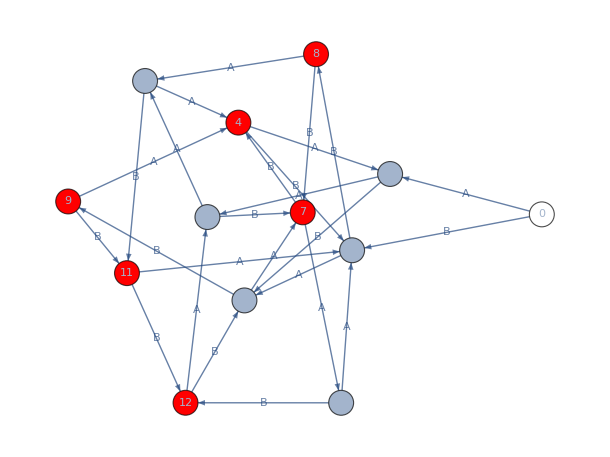

```mathematica
ShowGraph[δ,13,0,{4,7,8,9,11,12}]
```

### ¿Qué Strings acepta?

```mathematica
testset=StringJoin/@Tuples[{"A","B"},{4}];
testset⟦Flatten[Position[IsValid[δ,0,{4,7,8,9,11,12},#]&/@testset , True]]⟧//TableForm
```

AAAA
AAAB
AABB
ABAB
ABBA
ABBB
BAAB
BABA
BABB
BBAA
BBAB
BBBB

## Referencias